# The inheritance of local bifurcations in mass action networks

Murad Banaji^1, Balázs Boros^2, Josef Hofbauer^2

Mathematical Institute, University of Oxford, United Kingdom
 Department of Mathematics, University of Vienna, Austria

We compute the first and the second focal values of the homogeneous, rank-three mass action network that appears in Section 4.3 in the paper titled  “The inheritance of local bifurcations in mass action networks.”

## The smallest bimolecular mass-action system with a vertical Andronov-Hopf bifurcation

### The network

We have shown in
M. Banaji, B. Boros, J. Hofbauer
The smallest bimolecular mass-action system with a vertical Andronov-Hopf bifurcation
Applied Mathematics Letters, 143:108671, 2023
that the mass-action system



admits a vertical Andronov-Hopf bifurcation (and that this is the smallest such bimolecular system).
The bifurcation occurs at .

### Verify the transversality of the (vertical) Andronov-Hopf bifurcation

Below we verify the transversality of the bifurcation. For the theoretical details on transversality, see Section 2 in “The inheritance of local bifurcations in mass action networks.”

```mathematica
f=Subscript[κ, 1] x z{1,0,-1}+Subscript[κ, 2] x y{-1,1,0}+Subscript[κ, 3] y z{0,-1,-1}+Subscript[κ, 4]{0,0,2};
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
equilibrium=Normal[Simplify[Solve[f==0&&x>0&&y>0&&z>0&&κpositive,{x,y,z}]][[1]]];
J=D[f,{{x,y,z}}];
{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}=Simplify[CoefficientList[Collect[-CharacteristicPolynomial[J,λ],λ],λ]];
B2B1minusB0=Simplify[Subscript[b, 1] Subscript[b, 2]-Subscript[b, 0]];
Hopf={Subscript[κ, 1]->Subscript[κ, 2]+Subscript[κ, 3]};
HopfCondition=Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
h=Join[f,{B2B1minusB0}];
Dh=Simplify[D[h,{{x,y,z,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}}]/.equilibrium/.Hopf,HopfCondition];
Reduce[Simplify[Det[Dh[[{1,2,3,4},{1,2,3,4}]]]]!=0&&HopfCondition]
```

κ_2>0&&κ_3>0&&κ_4>0

## Andronov-Hopf bifurcation in the homogenised network

### The network

Homogenisation of the above network results in the mass-action system



Below we analyse the Andronov-Hopf bifurcation that is inherited from the 3d system.

### The ray of positive equilibria

Since the molecularity of every complex is the same (namely, two), the stoichiometric classes are given by  for . Furthermore, since the r.h.s. is homogeneous (of degree two), the phase portrait is the same (up to scaling) in every stoichiometric class. Hence, the set of positive equilibria is a ray.

```mathematica
f=Subscript[κ, 1] x z{1,0,-1,0}+Subscript[κ, 2] x y{-1,1,0,0}+Subscript[κ, 3] y z{0,-1,-1,2}+Subscript[κ, 4] w^2{0,0,2,-2};
equilibrium=Normal[Simplify[Solve[f==0&&w==t>0&&x>0&&y>0&&z>0&&w>0&&κpositive,{x,y,z,w}]][[1]]];
Print["r.h.s.: ",MatrixForm[f]];
Print["equilibrium ray: ",equilibrium];
```

r.h.s.: (x z κ_1-x y κ_2
x y κ_2-y z κ_3
-x z κ_1-y z κ_3+2 w^2 κ_4
2 y z κ_3-2 w^2 κ_4)

equilibrium ray: {x→t √((κ_3 κ_4)/(κ_1 κ_2)),y→t √((κ_1 κ_4)/(κ_2 κ_3)),z→t √((κ_2 κ_4)/(κ_1 κ_3)),w→t}

### Fix a stoichiometric class and eliminate

W.l.o.g. we restrict our attention to the stoichiometric class that has the above equilibrium with . Further, we eliminate the variable  using the conservation law.

```mathematica
tsubst={t->√((Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3])/Subscript[κ, 4])};
csubst={c->(x+y+z+w/.equilibrium)};
ff=Simplify[f[[{1,2,3}]]/.{w->c-x-y-z}/.csubst/.tsubst,κpositive];
equil=Normal[Solve[ff==0&&κpositive&&x>0&&y>0&&z>0&&x+y+z<Simplify[(c/.csubst/.tsubst),κpositive],{x,y,z}][[1]]];
Print["r.h.s. of the reduced system: ",MatrixForm[ff]];
Print["the unique positive equilibrium: ",equil];
```

r.h.s. of the reduced system: (x (z κ_1-y κ_2)
y (x κ_2-z κ_3)
-x z κ_1-y z κ_3+2 (-x-y-z+κ_1+κ_2+κ_3+√((κ_1 κ_2 κ_3)/κ_4))^2 κ_4)

the unique positive equilibrium: {x→κ_3,y→κ_1,z→κ_2}

### The Jacobian matrix and higher order derivatives at the positive equilibrium

```mathematica
A=Simplify[D[ff,{{x,y,z}}]/.equil,κpositive];

Idx[set_,n_]:=Module[{seq},seq=(Table[Count[set,i],{i,n}]/.List->Sequence);seq];

derivatives={};
order=2;
n=3;
For[i=0,i≤order,i++,For[j=0,j≤order-i,j++,For[k=0,k≤order-i-j,k++,
deriv=Simplify[D[ff,{x,i},{y,j},{z,k}]/.equil];
derivatives=Join[derivatives,Simplify[{Subscript[F, i,j,k]->deriv[[1]],Subscript[G, i,j,k]->deriv[[2]],Subscript[H, i,j,k]->deriv[[3]]}]];
]]];
B[x_,y_]:=Sum[{Subscript[F, Idx[{k,l},n]],Subscript[G, Idx[{k,l},n]],Subscript[H, Idx[{k,l},n]]}x[[k]]y[[l]]/.derivatives,{k,n},{l,n}];
CC[x_,y_,z_]:={0,0,0}; (* due to the bimolecularity all derivatives of order 3 and higher vanish *)
```

### The Routh-Hurwitz criterion

```mathematica
{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}=Simplify[CoefficientList[Collect[-CharacteristicPolynomial[A,λ],λ],λ]];
A2A1minusA0=Simplify[Subscript[a, 1] Subscript[a, 2]-Subscript[a, 0]];
RouthHurwitz=Simplify[Solve[A2A1minusA0==0&&Subscript[a, 0]>0&&Subscript[a, 2]>0&&κpositive,Subscript[κ, 4]][[1]]];
Hopf=Normal[RouthHurwitz];
HopfCondition=FullSimplify[RouthHurwitz[[1]][[2]][[2]]];
Print["pair of purely imaginary eigenvalues at ",Hopf," assuming ",HopfCondition];
```

pair of purely imaginary eigenvalues at {κ_4→(κ_1 (-κ_1+κ_2+κ_3)^2)/(16 κ_2 κ_3)} assuming κ_2>0&&κ_3>0&&κ_1>κ_2+κ_3

### Left and right eigenvectors of the Jacobian matrix

We eliminate  in the Jacobian matrix using the Routh-Hurwitz criterion. Then we find the left and right eigenvectors that are needed when computing the first focal value (see e.g. http://www.scholarpedia.org/article/Andronov-Hopf_bifurcation).

```mathematica
AA=Simplify[A/.Hopf,HopfCondition];
mtx=AA-ω ⅈ IdentityMatrix[n];
q=Simplify[NullSpace[mtx[[Range[1,n-1]]]][[1]]];
mtx=AAᵀ-ω ⅈ IdentityMatrix[n];
pconj=Simplify[NullSpace[mtx[[Range[1,n-1]]]][[1]]];
normalize=FullSimplify[pconj.q];
pconj=pconj/normalize;
qconj=FullSimplify[q*,ω>0&&κpositive];
```

### The first focal value ()

We now compute . It takes about 10-20 seconds.

```mathematica
Subscript[v, 1]=CC[q,q,qconj];
Subscript[v, 2]=Simplify[B[q,Inverse[-AA].B[q,qconj]]];
Subscript[v, 3]=Simplify[B[qconj,Inverse[2I ω IdentityMatrix[n]-AA].B[q,q]]];
Subscript[c, 1]=Simplify[pconj.(1/2 Subscript[v, 1]+Subscript[v, 2]+1/2 Subscript[v, 3])];
L1κω=Simplify[ComplexExpand[Re[Subscript[c, 1]]],ω>0&&κpositive];
ωsubst={ω->Simplify[√(Det[AA]/Tr[AA])]};
L1κ=FullSimplify[L1κω/.Hopf/.ωsubst];
Print[" equals   ",L1κ];
```

equals   -(κ_1 (κ_1-κ_2-κ_3) (κ_1+κ_2-κ_3)^2 κ_3^2 (5 κ_1^3+2 κ_1^2 (-3 κ_2+κ_3)+4 κ_2 κ_3 (-κ_2+κ_3)+κ_1 (-7 κ_2^2+6 κ_2 κ_3-3 κ_3^2)))/(8 κ_2 (κ_1-κ_3)^2 (κ_1 (κ_1-κ_2)^2+(2 κ_1^2-κ_1 κ_2+κ_2^2) κ_3+(κ_1-κ_2) κ_3^2) (κ_1^3+4 κ_2 (κ_2-κ_3) κ_3+2 κ_1^2 (-κ_2+κ_3)+κ_1 (κ_2+κ_3)^2))

### Analyse the sign of

We start with omitting the denominator (which is positive for ) and a positive factor in the enumerator.

```mathematica
L1=Numerator[L1κ/(Subscript[κ, 1](Subscript[κ, 1]-Subscript[κ, 2]-Subscript[κ, 3]) (Subscript[κ, 1]+Subscript[κ, 2]-Subscript[κ, 3])^2 Subscript[κ, 3]^2)];
Print["the part of  that determines its sign: ",L1];
```

the part of  that determines its sign: -5 κ_1^3-2 κ_1^2 (-3 κ_2+κ_3)-4 κ_2 κ_3 (-κ_2+κ_3)-κ_1 (-7 κ_2^2+6 κ_2 κ_3-3 κ_3^2)

W.l.o.g. we may set one of  equal to . Since  is cubic in  and only quadratic in  and , we set . Then we analyse the expression in the open triangle .

```mathematica
L1neg=Reduce[(L1/.{Subscript[κ, 1]->1})<0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 2]+Subscript[κ, 3]<1];
L1zer=Reduce[(L1/.{Subscript[κ, 1]->1})==0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 2]+Subscript[κ, 3]<1,Subscript[κ, 3]];
L1pos=Reduce[(L1/.{Subscript[κ, 1]->1})>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 2]+Subscript[κ, 3]<1];
Print[" negative: ",L1neg];
Print[" vanishes: ",L1zer];
Print[" positive: ",L1pos];
```

negative: (0<κ_2≤1/7 (-3+2 √11)&&0<κ_3<1-κ_2)||(1/7 (-3+2 √11)<κ_2<Root0.626Root[1+2 #1-7 #1^2+2 #1^3&,2]0.6258859462044956&&(-1-3 κ_2+2 κ_2^2)/(-3+4 κ_2)-2 √((4-8 κ_2+2 κ_2^2+4 κ_2^3+κ_2^4)/(-3+4 κ_2)^2)<κ_3<1-κ_2)

vanishes: 1/7 (-3+2 √11)<κ_2<Root0.626Root[1+2 #1-7 #1^2+2 #1^3&,2]0.6258859462044956&&κ_3==(-1-3 κ_2+2 κ_2^2)/(-3+4 κ_2)-2 √((4-8 κ_2+2 κ_2^2+4 κ_2^3+κ_2^4)/(-3+4 κ_2)^2)

positive: (1/7 (-3+2 √11)<κ_2≤Root0.626Root[1+2 #1-7 #1^2+2 #1^3&,2]0.6258859462044956&&0<κ_3<(-1-3 κ_2+2 κ_2^2)/(-3+4 κ_2)-2 √((4-8 κ_2+2 κ_2^2+4 κ_2^3+κ_2^4)/(-3+4 κ_2)^2))||(Root0.626Root[1+2 #1-7 #1^2+2 #1^3&,2]0.6258859462044956<κ_2<1&&0<κ_3<1-κ_2)

Hence,  can have any sign. Below we visualise this.

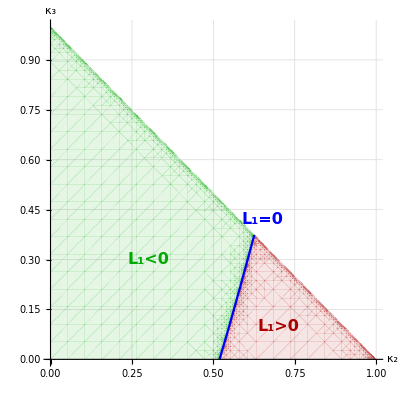

```mathematica
rneg=RegionPlot[L1neg,{Subscript[κ, 2],0,1},{Subscript[κ, 3],0,1},PlotStyle->{Darker[Green],Opacity[0.1]},GridLines->Automatic,MaxRecursion->6,BoundaryStyle->None,Frame->None,AxesLabel->{Style[,Bold,16],Style[,Bold,16]},Axes->True];
rpos=RegionPlot[L1pos,{Subscript[κ, 2],0,1},{Subscript[κ, 3],0,1},PlotStyle->{Darker[Red],Opacity[0.1]},MaxRecursion->6,BoundaryStyle->None];

L1zersolve=Solve[(L1/.{Subscript[κ, 1]->1})==0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 2]+Subscript[κ, 3]<1,Subscript[κ, 3]][[1]];
curve=Normal[L1zersolve[[1]][[2]]];
min=L1zersolve[[1]][[2]][[2]][[1]];
max=L1zersolve[[1]][[2]][[2]][[5]];
rzer=Plot[curve,{Subscript[κ, 2],min,max},PlotStyle->Blue];

txt=Graphics[{Text[Style["L_1<0",Darker[Green],Bold,16],{0.3,0.3}],Text[Style["L_1=0",Blue,Bold,16],{0.65,0.42}],Text[Style["L_1>0",Darker[Red],Bold,16],{0.7,0.1}]}];

Show[rneg,rpos,rzer,txt]
```

### The second focal value ()

Below we compute the second focal value along the curve in parameter space, where the first focal value vanishes (note: the process takes about 1-2 minutes). We find that  changes sign. Where , a nondegenerate Bautin bifurcation occurs. To understand the behaviour at and near the single point in parameter space with , one would need to compute the third focal value, which we leave as an open question.

equals -(((1+κ_2-κ_3)^2 κ_3 (-(-1+κ_3)^3 κ_3 (1+κ_3)^10 (131+1475 κ_3-2035 κ_3^2+717 κ_3^3)+κ_2 (-1+κ_3)^2 (1+κ_3)^8 (-280-2292 κ_3-10791 κ_3^2+34047 κ_3^3-20298 κ_3^4+6046 κ_3^5-11063 κ_3^6+7319 κ_3^7)+κ_2^16 (392+6347 κ_3+49881 κ_3^2+218545 κ_3^3+527947 κ_3^4+701760 κ_3^5+519824 κ_3^6+203648 κ_3^7+32256 κ_3^8)-κ_2^15 (3976+54068 κ_3+354533 κ_3^2+1318213 κ_3^3+2954387 κ_3^4+4200039 κ_3^5+3949968 κ_3^6+2628528 κ_3^7+1163776 κ_3^8+225792 κ_3^9)+κ_2^14 (17192+201016 κ_3+1150789 κ_3^2+3858577 κ_3^3+8357361 κ_3^4+12882975 κ_3^5+14456810 κ_3^6+10575152 κ_3^7+5668208 κ_3^8+2754432 κ_3^9+645120 κ_3^10)-κ_2^2 (1+κ_3)^6 (-3416-7256 κ_3-243 κ_3^2+170387 κ_3^3-270516 κ_3^4+101160 κ_3^5+153558 κ_3^6-450418 κ_3^7+557300 κ_3^8-294952 κ_3^9+17973 κ_3^10+26423 κ_3^11)-κ_2^13 (39144+424268 κ_3+2293753 κ_3^2+7252657 κ_3^3+15681533 κ_3^4+26478445 κ_3^5+31104078 κ_3^6+26650218 κ_3^7+16109424 κ_3^8+7019984 κ_3^9+3572736 κ_3^10+903168 κ_3^11)+κ_2^12 (40936+538892 κ_3+3031245 κ_3^2+9436909 κ_3^3+22821095 κ_3^4+39101234 κ_3^5+49310603 κ_3^6+47604437 κ_3^7+28421257 κ_3^8+12083664 κ_3^9+5770912 κ_3^10+2959104 κ_3^11+451584 κ_3^12)+κ_2^3 (1+κ_3)^4 (-18424-5692 κ_3+115813 κ_3^2+307593 κ_3^3+62521 κ_3^4-515315 κ_3^5+947318 κ_3^6-2711362 κ_3^7+3200622 κ_3^8-1871342 κ_3^9+997045 κ_3^10-691927 κ_3^11+184769 κ_3^12+57773 κ_3^13)+κ_2^11 (19096-328436 κ_3-2264289 κ_3^2-8776945 κ_3^3-25936551 κ_3^4-44173299 κ_3^5-65994811 κ_3^6-60341187 κ_3^7-44378901 κ_3^8-16820261 κ_3^9+56672 κ_3^10-3894752 κ_3^11-1658880 κ_3^12+451584 κ_3^13)+κ_2^10 (-125048-264648 κ_3-370511 κ_3^2+5339221 κ_3^3+18705413 κ_3^4+45886649 κ_3^5+63311343 κ_3^6+72323471 κ_3^7+51062455 κ_3^8+20089963 κ_3^9+698716 κ_3^10-6510368 κ_3^11+3666400 κ_3^12+13056 κ_3^13-903168 κ_3^14)-κ_2^4 (1+κ_3)^2 (-56952+56788 κ_3+605073 κ_3^2+1049723 κ_3^3+2427020 κ_3^4-738749 κ_3^5+401655 κ_3^6-5184794 κ_3^7+1972112 κ_3^8+625458 κ_3^9-830393 κ_3^10+2269551 κ_3^11-3151348 κ_3^12+1329655 κ_3^13-64127 κ_3^14+125936 κ_3^15)+κ_2^9 (179256+1072468 κ_3+3420683 κ_3^2+1204995 κ_3^3-5509473 κ_3^4-36461521 κ_3^5-53708387 κ_3^6-69971699 κ_3^7-47424571 κ_3^8-27055863 κ_3^9-205476 κ_3^10+10039620 κ_3^11+2417184 κ_3^12-4239008 κ_3^13+1471488 κ_3^14+645120 κ_3^15)+κ_2^8 (-109032-1679094 κ_3-4949373 κ_3^2-9275525 κ_3^3-3218407 κ_3^4+10074848 κ_3^5+48869222 κ_3^6+44953034 κ_3^7+54276082 κ_3^8+13492878 κ_3^9+4460151 κ_3^10-1545629 κ_3^11-10507475 κ_3^12+3268064 κ_3^13+2847184 κ_3^14-1655424 κ_3^15-225792 κ_3^16)+κ_2^7 (-28952+1637956 κ_3+4734561 κ_3^2+12894625 κ_3^3+9678375 κ_3^4+5742811 κ_3^5-23163214 κ_3^6-41875854 κ_3^7-24999986 κ_3^8-23369390 κ_3^9+3058637 κ_3^10+1221549 κ_3^11-1161453 κ_3^12+5495103 κ_3^13-4174544 κ_3^14-341872 κ_3^15+795136 κ_3^16+32256 κ_3^17)-κ_2^6 (-115192+984664 κ_3+3607009 κ_3^2+9966925 κ_3^3+14048957 κ_3^4+6541919 κ_3^5-1684968 κ_3^6-26621470 κ_3^7-22379214 κ_3^8-6308314 κ_3^9+731985 κ_3^10+2279185 κ_3^11-3716983 κ_3^12+174931 κ_3^13+1935846 κ_3^14-1855728 κ_3^15+548432 κ_3^16+146048 κ_3^17)+κ_2^5 (-107576+276860 κ_3+2062277 κ_3^2+5334909 κ_3^3+10951737 κ_3^4+7225513 κ_3^5+379244 κ_3^6-9746912 κ_3^7-14043846 κ_3^8-4968402 κ_3^9+1699725 κ_3^10+5075181 κ_3^11-2284891 κ_3^12-3766035 κ_3^13+1666834 κ_3^14+604358 κ_3^15-87984 κ_3^16+200048 κ_3^17)))/(48 κ_2^3 (-1+κ_2-κ_3) (-1+κ_3)^4 ((1+κ_3)^2+κ_2^2 (1+9 κ_3)+κ_2 (-2+7 κ_3-9 κ_3^2)) ((1+κ_3)^2+κ_2^2 (1+4 κ_3)+κ_2 (-2+2 κ_3-4 κ_3^2))^3 (κ_2^2 (1+κ_3)+(1+κ_3)^2-κ_2 (2+κ_3+κ_3^2))^3))

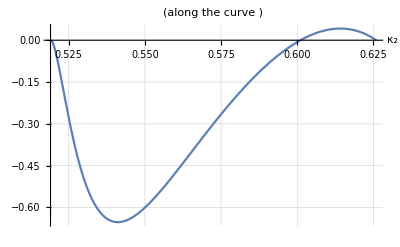

```mathematica
Id=IdentityMatrix[n];
κ1subst={Subscript[κ, 1]->1};
omega=(ω/.ωsubst/.κ1subst);
ωSQsubst={ω^2->omega^2,ω^3->omega^2 ω,ω^4->omega^4,ω^5->omega^4 ω,ω^6->omega^6,ω^7->omega^6 ω,ω^8->omega^8,ω^9->omega^8 ω,ω^10->omega^10};
invA=Simplify[Inverse[AA/.κ1subst]];
inv2=Simplify[Expand[Inverse[2 ω I Id-AA]]/.ωSQsubst/.κ1subst];
inv3=Simplify[Expand[Inverse[3 ω I Id-AA]]/.ωSQsubst/.κ1subst];

q=Simplify[q/.ωSQsubst/.κ1subst];
qconj=Simplify[qconj/.ωSQsubst/.κ1subst];
pconj=Simplify[pconj/.ωSQsubst/.κ1subst];

Subscript[h, 2,0]=Simplify[Expand[Simplify[inv2.B[q,q]/.Hopf/.κ1subst]]/.ωSQsubst];
Subscript[h, 1,1]=Simplify[Expand[-invA.B[q,qconj]]/.Hopf/.κ1subst/.ωSQsubst];
prec=Simplify[ComplexExpand[2 B[q,Subscript[h, 1,1]]+B[qconj,Subscript[h, 2,0]]]/.Hopf/.κ1subst/.ωSQsubst];
Subscript[c, 1]=I Simplify[ExpandAll[ComplexExpand[Im[1/2 (pconj.prec)]]]/.ωSQsubst];

invbig=Simplify[Expand[Simplify[Simplify[Inverse[Join[Join[ω I Id-AA,{q}ᵀ,2],{Join[pconj,{0}]}]]]/.ωSQsubst/.κ1subst]]/.ωSQsubst];
precminus2c1q=Simplify[Expand[Simplify[ExpandAll[prec-2 Subscript[c, 1] q]/.ωSQsubst]]];
h21=Simplify[Expand[Simplify[Simplify[invbig.Join[precminus2c1q,{0}]]/.ωSQsubst]]/.ωSQsubst];
Subscript[h, 2,1]=Join[h21[[1;;3]],{0}]; (* turns out the last entry vanishes when  *)
Subscript[h, 3,0]=Simplify[Expand[Simplify[inv3.(CC[q,q,q]+3 B[q,Subscript[h, 2,0]])/.Hopf/.κ1subst]]/.ωSQsubst];

Subscript[v, 1]=Simplify[3 B[Subscript[h, 2,0],Subscript[h, 1,1]]/.Hopf/.κ1subst];
Subscript[v, 2]=Simplify[Expand[Simplify[B[qconj,Subscript[h, 3,0]]/.Hopf/.κ1subst]]/.ωSQsubst];
Subscript[v, 3]=Simplify[Expand[Simplify[3 B[q,Subscript[h, 2,1]]/.Hopf/.κ1subst]]/.ωSQsubst];
Subscript[v, 4]=Simplify[Expand[-6 Subscript[c, 1] Subscript[h, 2,0]]/.ωSQsubst];
Subscript[h, 3,1]=Simplify[Expand[Simplify[Expand[inv2.(Subscript[v, 1]+Subscript[v, 2]+Subscript[v, 3]+Subscript[v, 4])]/.ωSQsubst]]/.ωSQsubst];

Subscript[v, 1]=Simplify[2B[Subscript[h, 1,1],Subscript[h, 1,1]]/.Hopf/.κ1subst];
Subscript[v, 2]=Simplify[Expand[Simplify[2 B[q,ComplexExpand[Subscript[h, 2,1]*]]/.Hopf/.κ1subst]]/.ωSQsubst];
Subscript[v, 3]=Simplify[Expand[Simplify[2 B[qconj,Subscript[h, 2,1]]/.Hopf/.κ1subst]]/.ωSQsubst];
Subscript[v, 4]=Simplify[Expand[Simplify[B[ComplexExpand[Subscript[h, 2,0]*],Subscript[h, 2,0]]/.Hopf/.κ1subst/.ωSQsubst]]/.ωSQsubst];
R={0,0,Simplify[Simplify[Subscript[v, 1][[3]]+Subscript[v, 2][[3]]+Subscript[v, 3][[3]]+Subscript[v, 4][[3]]]/.ωSQsubst]}; (* turns out the first and second entries vanish when  *)
Subscript[h, 2,2]=Simplify[-invA.R];

Subscript[v, 1]=Simplify[ComplexExpand[Re[Simplify[Simplify[pconj.(2 B[qconj,Subscript[h, 3,1]])/.Hopf/.κ1subst]/.ωSQsubst]]]/.ωSQsubst];
Subscript[v, 2]=Simplify[ComplexExpand[Re[Simplify[Simplify[pconj.(3B[q,Subscript[h, 2,2]])/.Hopf/.κ1subst]/.ωSQsubst]]]/.ωSQsubst];
Subscript[v, 3]=Simplify[ComplexExpand[Re[Simplify[Simplify[pconj.B[Subscript[h, 2,0]*,Subscript[h, 3,0]]/.Hopf/.κ1subst]/.ωSQsubst]]]/.ωSQsubst];
Subscript[v, 4]=Simplify[ComplexExpand[Re[Simplify[Simplify[pconj.(3 B[Subscript[h, 2,1]*,Subscript[h, 2,0]])/.Hopf/.κ1subst]/.ωSQsubst]]]/.ωSQsubst];
Subscript[v, 5]=Simplify[ComplexExpand[Re[Simplify[Simplify[pconj.(6 B[Subscript[h, 1,1],Subscript[h, 2,1]])/.Hopf/.κ1subst]/.ωSQsubst]]]/.ωSQsubst];

L2=Simplify[Subscript[v, 1]+Subscript[v, 2]+Subscript[v, 3]+Subscript[v, 4]+Subscript[v, 5]/.ωSQsubst];
Print[" equals ",L2];
Plot[L2/.{Subscript[κ, 3]->curve},{Subscript[κ, 2],min,max},GridLines->Automatic,PlotLabel->" (along the curve )",AxesLabel->{Style[,Bold,16],None}]
```

Next, we visualize in parameter space the signs of  and . In fact, the drawing is in the -plane (recall that  was eliminated using the Routh-Hurwitz criterion, and we assumed w.l.o.g. that ). Since we do compute symbolically the single point in parameter space, where both  and  vanish, the process takes about 40-50 seconds.

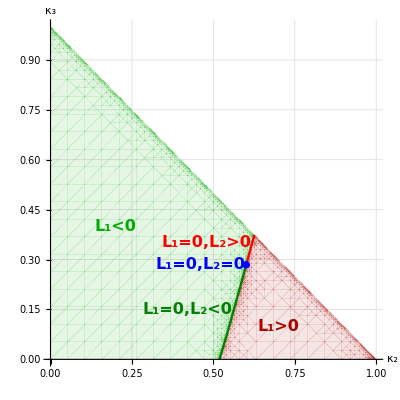

```mathematica
κ2TH=Solve[Simplify[L2/.{Subscript[κ, 3]->curve},min<Subscript[κ, 2]<max]==0&&min<Subscript[κ, 2]<max,Subscript[κ, 2]][[1]];
κ3TH={Subscript[κ, 3]->FullSimplify[curve/.κ2TH]};
TH={Subscript[κ, 2],Subscript[κ, 3]}/.κ2TH/.κ3TH;
plTH=ListPlot[{TH},PlotStyle->Blue];
L2neg=Plot[curve,{Subscript[κ, 2],min,TH[[1]]},PlotStyle->RGBColor["Green"]];
L2pos=Plot[curve,{Subscript[κ, 2],TH[[1]],max},PlotStyle->Red];

txtL2=Graphics[{Text[Style["L_1<0",Darker[Green],Bold,16],{0.2,0.4}],Text[Style["L_1=0,L_2=0",Blue,Bold,16],{0.46,TH[[2]]}],Text[Style["L_1=0,L_2>0",Red,Bold,16],{0.48,0.35}],Text[Style["L_1=0,L_2<0",RGBColor["Green"],Bold,16],{0.42,0.15}],Text[Style["L_1>0",Darker[Red],Bold,16],{0.7,0.1}]}];

Show[rneg,rpos,L2neg,L2pos,plTH,txtL2]
```

### Verify the transversality of the Andronov-Hopf bifurcation

We append the vector field with the Routh-Hurwitz condition and thus get , see Section 2 in “The inheritance of local bifurcations in mass action networks.” Then we compute the derivative at the equilibrium and the critical parameter value. Thus, we obtain an  matrix (here,  is the number of species,  is the number of rate constants, and  is the codimension).

```mathematica
J=D[ff,{{x,y,z}}];
{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}=Simplify[CoefficientList[Collect[-CharacteristicPolynomial[J,λ],λ],λ]];
B2B1minusB0=Simplify[Subscript[b, 1] Subscript[b, 2]-Subscript[b, 0]];
h=Join[ff,{B2B1minusB0}];
Dh=Simplify[D[h,{{x,y,z,Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4]}}]/.equil/.Hopf,HopfCondition];
```

We check the nonsingularity of the  by  matrix formed by the 1st, 2nd, 3rd, and 7th column of  at every  with .

```mathematica
Reduce[Simplify[Det[Dh[[{1,2,3,4},{1,2,3,7}]]]]!=0&&HopfCondition,Subscript[κ, 1]]
```

κ_2>0&&κ_3>0&&κ_1>κ_2+κ_3

### Verify the transversality of the Bautin bifurcation

For the transversality of the Bautin bifurcation, it suffices to check that  (as a function of, say, ) changes sign transversally. I.e., its derivative w.r.t. κ_2 is nonzero when .

```mathematica
der=Simplify[D[L1,{Subscript[κ, 2]}]/.{Subscript[κ, 1]->1}/.{Subscript[κ, 3]->curve},min<Subscript[κ, 2]<max];
Reduce[der!=0&&min<Subscript[κ, 2]<max]
```

1/7 (-3+2 √11)<κ_2<Root0.626Root[1+2 #1-7 #1^2+2 #1^3&,2]0.6258859462044956